Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

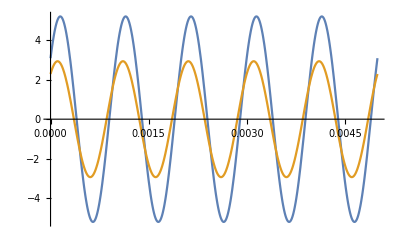

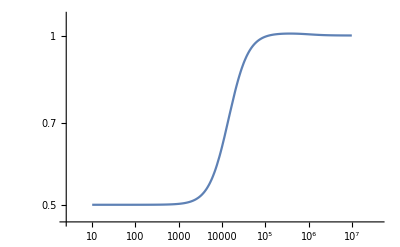

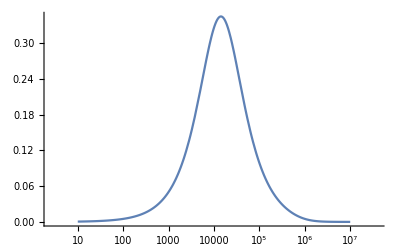

```mathematica
R1=10000;
R2=10000;
C1=10*10^-9;
L1=10*10^-3;
uZ=4.2+3.1ⅉ;

uzel1=iUf==iC1f+iR1f;
uzel2=iC1f+iR1f==iR2f;
uzel3=iR2f==iL1f;

rovR1=u1f-u2f==R1*iR1f;
rovR2=u2f-u3f==R2*iR2f;
rovL1=u3f==ⅉ*ω*L1*iL1f;
rovC1=iC1f==ⅉ*ω*C1*(u1f-u2f);
rovU=u1f==uZ;

rce={uzel1,uzel2,uzel3,rovC1,rovL1,rovR1,rovR2,rovU};
vysledek=Solve[rce];
Plot[{Im[u1f*ⅇ^(ⅉ*ω*t)/.vysledek/.ω->1000*2*Pi],Im[u2f*ⅇ^(ⅉ*ω*t)/.vysledek/.ω->1000*2*Pi]},{t,0,0.005}]
prenos=u2f/u1f/.vysledek;
LogLogPlot[Abs[prenos],{ω,10,10^7}]
LogLinearPlot[Arg[prenos],{ω,10,10^7}]
```

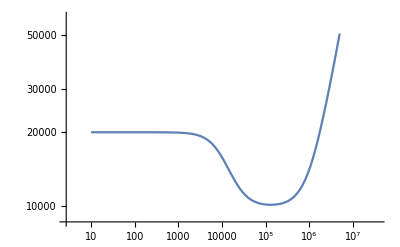

```mathematica
(* IMPEDANCE *)
ZR1=10000;
ZR2=10000;
ZL1=ⅉ*ω*0.01;
ZC1=1/(ⅉ*ω*10*10^-9);
ZD=ZR2+ZL1;
ZH=1/(1/ZR1+1/ZC1);
Zcelk=ZH+ZD;
LogLogPlot[Abs[Zcelk], {ω,10,10^7}]
```

```mathematica
(* 8.5 Uout/Uin *)
(* 8.6 Z=Uf/If *)
```